## Import data files and create interpolation objects

Native Coulomb wave form factors span the range E = 1 eV to 109.648 eV and:
for 4e2, q = 1 to 33.99 keV;
for 5e1, q = 1 to 33.99 keV;
for 5e2, q = 1 to 33.99 keV;
for 6a, q = 1 to 38.89 keV.
q is the momentum transfer [in keV] and E is the electron kinetic energy [in keV].

For higher values of q than those above (where the form factor is very very small), we also give form factors where we match onto the (rescaled) plane wave results. The plots at the bottom of the notebook show this extrapolation.

### Coulomb wave

```mathematica
SetDirectory[NotebookDirectory[]];
LC4H104e2grid=Import["C4H10_CW_4e2_grid.dat"];
LC4H105e1grid=Import["C4H10_CW_5e1_grid.dat"];
LC4H105e2grid=Import["C4H10_CW_5e2_grid.dat"];
LC4H106agrid=Import["C4H10_CW_6a_grid.dat"];
ResetDirectory[];

fC4H104e2=Interpolation[LC4H104e2grid,InterpolationOrder->1]
fC4H105e1=Interpolation[LC4H105e1grid,InterpolationOrder->1]
fC4H105e2=Interpolation[LC4H105e2grid,InterpolationOrder->1]
fC4H106a=Interpolation[LC4H106agrid,InterpolationOrder->1]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

«1 more identical outputs»

### Coulomb wave + matched rescaled Plane wave at high q

```mathematica
SetDirectory[NotebookDirectory[]];
LC4H10CWPW4e2grid=Import["C4H10_4e2_grid_PW_largeQ.dat"];
LC4H10CWPW5e1grid=Import["C4H10_5e1_grid_PW_largeQ.dat"];
LC4H10CWPW5e2grid=Import["C4H10_5e2_grid_PW_largeQ.dat"];
LC4H10CWPW6agrid=Import["C4H10_6a_grid_PW_largeQ.dat"];
ResetDirectory[];

fC4H10CWPW4e2=Interpolation[LC4H10CWPW4e2grid,InterpolationOrder->1]
fC4H10CWPW5e1=Interpolation[LC4H10CWPW5e1grid,InterpolationOrder->1]
fC4H10CWPW5e2=Interpolation[LC4H10CWPW5e2grid,InterpolationOrder->1]
fC4H10CWPW6a=Interpolation[LC4H10CWPW6agrid,InterpolationOrder->1]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

«1 more identical outputs»

### Plots

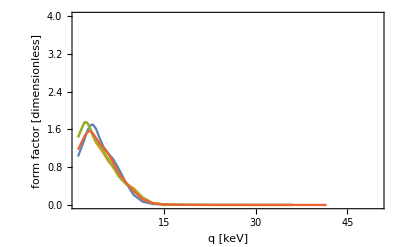

```mathematica
EtestkeV=0.025;

Plot[{fC4H104e2[q,EtestkeV],fC4H105e1[q,EtestkeV],fC4H105e2[q,EtestkeV],fC4H106a[q,EtestkeV]},{q,1,50},PlotRange->{{1,50},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"}]
```

### Plots - showing the plane wave extrapolation in black

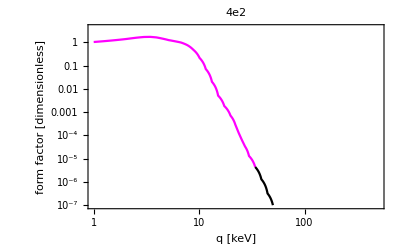

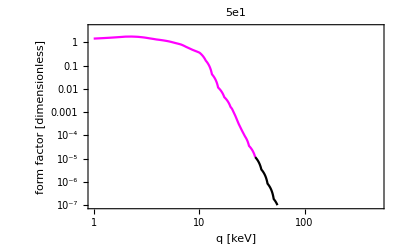

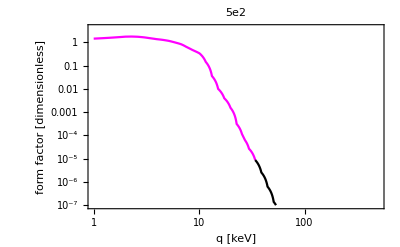

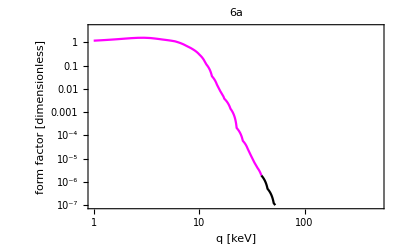

```mathematica
EtestkeV=0.025;

Show[LogLogPlot[{fC4H104e2[q,EtestkeV]},{q,1,LC4H104e2grid[[-1,1]]},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->Magenta],LogLogPlot[{fC4H10CWPW4e2[q,EtestkeV]},{q,LC4H104e2grid[[-1,1]],200},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->{Black}],PlotLabel->"4e2"]

Show[LogLogPlot[{fC4H105e1[q,EtestkeV]},{q,1,LC4H105e1grid[[-1,1]]},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->Magenta],LogLogPlot[{fC4H10CWPW5e1[q,EtestkeV]},{q,LC4H105e1grid[[-1,1]],200},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->{Black}],PlotLabel->"5e1"]

Show[LogLogPlot[{fC4H105e2[q,EtestkeV]},{q,1,LC4H105e2grid[[-1,1]]},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->Magenta],LogLogPlot[{fC4H10CWPW5e2[q,EtestkeV]},{q,LC4H105e2grid[[-1,1]],200},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->{Black}],PlotLabel->"5e2"]


Show[LogLogPlot[{fC4H106a[q,EtestkeV]},{q,1,LC4H106agrid[[-1,1]]},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->Magenta],LogLogPlot[{fC4H10CWPW6a[q,EtestkeV]},{q,LC4H106agrid[[-1,1]],200},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->{Black}],PlotLabel->"6a"]
```

### Check numerical accuracy - should be the same result

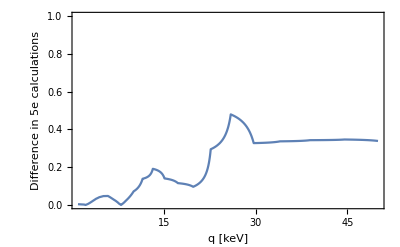

```mathematica
Plot[{Abs[fC4H10CWPW5e1[q,EtestkeV]-fC4H10CWPW5e2[q,EtestkeV]]/fC4H10CWPW5e2[q,EtestkeV]},{q,1,50},PlotRange->{{1,50},{0,1}},Frame->True,FrameLabel->{"q [keV]","Difference in 5e calculations"}]
```